30000

0

28090

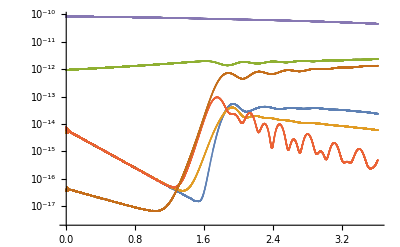

```mathematica
(*Run Constants*)
NN=32;
MInt="9,983707801310956e-06";
Mh="1,9321253110041805e-08";
CO=160;
dt=0.1;
SpecialComment="";
EfoldsToEOI=0.;
Comment="_MInt="<>MInt<>"_Mh="<>Mh<>"_CO="<>StringReplace[ToString[CO],"."->","]<>"_N="<>StringReplace[ToString[NN],"."->","]<>SpecialComment;

(*extensions to download the files from Lattice Easy and to write the result*)
dir="/home/michal/Documents/gd_simulation/Results/ResultsNewN64/";
SetDirectory["/home/michal/Documents/gd_simulation/Results/ResultsNewN64"];
intableenergy=ReadList[dir<>"energyData"<>Comment<>".dat",Table[Real,{7}]];
PointsNumber=Length[intableenergy]
TimeEnd=0
Do[If[Log[intableenergy[[time,1]]]<3.62,{TimeEnd=time,Exit},{}],{time,1,PointsNumber}]
PointsNumber=TimeEnd

Phikinetictable=Table[{Log[intableenergy[[time,1]]]-EfoldsToEOI,intableenergy[[time,2]]},{time,1,PointsNumber}];
Chikinetictable=Table[{Log[intableenergy[[time,1]]]-EfoldsToEOI,intableenergy[[time,3]]},{time,1,PointsNumber}];

Phigradienttable=Table[{Log[intableenergy[[time,1]]]-EfoldsToEOI,intableenergy[[time,4]]},{time,1,PointsNumber}];
Chigradienttable=Table[{Log[intableenergy[[time,1]]]-EfoldsToEOI,intableenergy[[time,5]]},{time,1,PointsNumber}];
Inflatonpotentialtable=Table[{Log[intableenergy[[time,1]]]-EfoldsToEOI,intableenergy[[time,6]]},{time,1,PointsNumber}];
Chipotentialtable=Table[{Log[intableenergy[[time,1]]]-EfoldsToEOI,intableenergy[[time,7]]},{time,1,PointsNumber}];
energytable=Table[{Log[intableenergy[[time,1]]]-EfoldsToEOI,Phikinetictable[[time,2]]+Chikinetictable[[time,2]]+Phigradienttable[[time,2]]+Chigradienttable[[time,2]]+Inflatonpotentialtable[[time,2]]+Chipotentialtable[[time,2]]},{time,1,PointsNumber}];
Logenergytable=Table[{Log[intableenergy[[time,1]]],Log[energytable[[time,2]]]},{time,1,PointsNumber}];
  
Needs["MaTeX`"];
LogManyEnergyplot=Framed[ListLogPlot[{Phigradienttable,Chigradienttable,Phikinetictable,Chikinetictable,Inflatonpotentialtable,Chipotentialtable},AxesLabel->{MaTeX["N",FontSize->16],MaTeX["E",FontSize->16]},PlotLegends->SwatchLegend[{MaTeX["E_{gr,\\phi}",FontSize->16],MaTeX["E_{gr,\\chi}",FontSize->16],MaTeX["E_{k,\\phi}",FontSize->16],MaTeX["E_{k,\\chi}",FontSize->16],MaTeX["E_{V,\\phi}",FontSize->16],MaTeX["E_{V,\\chi}",FontSize->16]},LegendMarkerSize->10,LegendMarkers->"Bubble"],LabelStyle->Directive[FontSize->14],PlotRange->All]]
gfxname=FileBaseName["LogManyEnergyPlot2"<>Comment];
Export[gfxname<>".pdf",LogManyEnergyplot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600];   

(*
LogPotplot=ListLogPlot[{potentialtable},AxesLabel->{"N","V"},PlotRange->All]
gfxname=FileBaseName["LogPotentialPlot"<>Comment];
Export[gfxname<>".png",LogPotplot];   


ChiGradientEnergyplot=ListLogPlot[{Chigradienttable},AxesLabel->{"N","ChiGradientEnergy [M_Pl]"},PlotRange->All]
gfxname=FileBaseName["ChiGradientEnergyPlot"<>Comment];
Export[gfxname<>".png",ChiGradientEnergyplot];   

PhiGradientEnergyplot=ListLogPlot[{Phigradienttable},AxesLabel->{"N","PhiGradientEnergy [M_Pl]"},PlotRange->All]
gfxname=FileBaseName["PhiGradientEnergyPlot"<>Comment];
Export[gfxname<>".png",PhiGradientEnergyplot];   


ChiKineticEnergyplot=ListLogPlot[{Chikinetictable},AxesLabel->{"N","ChiKineticEnergy [M_Pl]"},PlotRange->All]
gfxname=FileBaseName["ChiKineticEnergyPlot"<>Comment];
Export[gfxname<>".png",ChiKineticEnergyplot]; 

PhiKineticEnergyplot=ListLogPlot[{Phikinetictable},AxesLabel->{"N","PhiKineticEnergy [M_Pl]"},PlotRange->All]
gfxname=FileBaseName["PhiKineticEnergyPlot"<>Comment];
Export[gfxname<>".png",PhiKineticEnergyplot];  *)
```